```mathematica
GetDetritusEnergies[frameNo_]:=Module[{path,i,items,ptE},
path = StringForm["``\\output\\frame``.json",dir,frameNo];
{i}=Import[path//ToString];
items = "Items"/.i;
ptE={"pt","e"}/.items;
Cases[ptE,{2,x_}->x]
]
```

115500

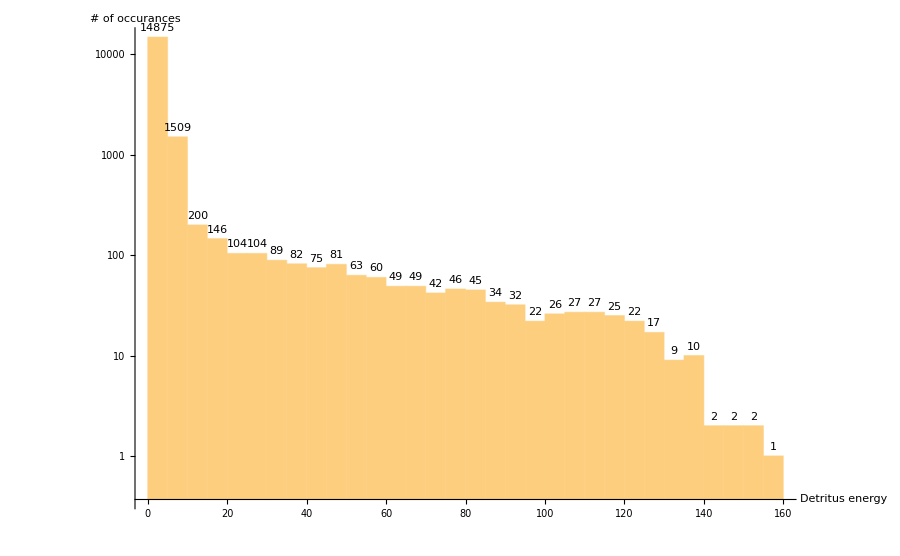

Mean: | 6.65852
Median: | 1.97598
Max: | 158.91

```mathematica
frame=115500
es =GetDetritusEnergies[frame];
Histogram[es,30,
PlotRange->All,
ScalingFunctions->"Log",
AxesLabel->{"Detritus energy","# of occurances"},
LabelingFunction->Above,
ImageSize->900]
({{"Mean:", es//Mean}, {"Median:", es//Median}, {"Max:", es//Max}})//TableForm
```